```mathematica
2/l*Integrate[Cos[(π/4+(n*π)/l)*x],{x,0,l},Assumptions->l>0&&n∈Integers]
```

(8 Sin[(l π)/4+n π])/(l π+4 n π)

```mathematica
%41/.l->q
```

(8 Sin[n π+(π q)/4])/(4 n π+π q)

```mathematica
%42/(π/4+(n*π)/q)
```

(8 Sin[n π+(π q)/4])/((π/4+(n π)/q) (4 n π+π q))

```mathematica
Simplify[(8 Sin[n π+(π q)/4])/((π/4+(n π)/q) (4 n π+π q))]
```

(32 q Sin[1/4 π (4 n+q)])/(π^2 (4 n+q)^2)

```mathematica
A[n_]=(8 Sin[n π+π/4])/(4 n π+π)
```

(8 Sin[π/4+n π])/(π+4 n π)

```mathematica
A[1]
```

-(4 √2)/(5 π)

```mathematica
TrigReduce[(2 l^2 (2 Cos[n π]+(1+2 n) π Sin[n π]))/(π+2 n π)^2]
```

(2 (2 l^2 Cos[n π]+l^2 π Sin[n π]+2 l^2 n π Sin[n π]))/((1+2 n)^2 π^2)

```mathematica
D[u[x,t],x]/.x->0
```

0

```mathematica
u[x_,t_]=Cos[√(1+(a^2*π^2)/l^2)t]*Cos[π/l*x]
```

Cos[√(1+(a^2 π^2)/l^2) t] Cos[(π x)/l]

```mathematica
D[u[x,t],{t,2}]-a^2*D[u[x,t],{x,2}]+u[x,t]//Simplify
```

0

```mathematica
b[n_]=1/π Integrate[x*Sin[n*x],{x,-π,π}]
```

(-2 n π Cos[n π]+2 Sin[n π])/(n^2 π)

```mathematica
b[1]
```

2

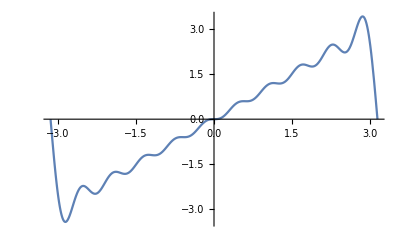

```mathematica
Plot[Sum[b[i]*Sin[i*x],{i,1,10}]//N,{x,-π,π}]
```

```mathematica
B[n_]=(32 Sin[1/4 π (4 n+1)])/(π^2 (4 n+1)^2)
```

(32 Sin[1/4 (1+4 n) π])/((1+4 n)^2 π^2)

```mathematica
Sum[A[i],{i,1,100}]//N
```

-0.237299

```mathematica
B[1]
```

-(16 √2)/(25 π^2)

```mathematica
β[n_]=π/4+n*π
```

π/4+n π

```mathematica
β[1]
```

(5 π)/4

```mathematica
Term[n_]=(A[n]*Cos[β[n]*t]+B[n]*Sin[β[n]*t])*Cos[β[n] x]
```

Cos[x β[n]] (A[n] Cos[t β[n]]+(32 Sin[1/4 (1+4 n) π] Sin[t β[n]])/((1+4 n)^2 π^2))

```mathematica
Sum[Term[i],{i,1,10}]//N//Simplify
```

Cos[0.860334 x] (1.11913 Cos[0.860334 t]-0.0917055 Sin[0.860334 t])+Cos[3.42562 x] (-0.151692 Cos[3.42562 t]+0.0283042 Sin[3.42562 t])+Cos[6.4373 x] (0.0465941 Cos[6.4373 t]-0.0135659 Sin[6.4373 t])

```mathematica
usol=NDSolveValue[{D[u[x,t],{t,2}]==D[u[x,t],{x,2}],(D[u[x,t],x]/.x->0)==0,(D[u[x,t],x]/.x->1)+u[1,t]==0,u[x,0]==1,(D[u[x,t],t]/.t->0)==1},u,{x,0,1},{t,0,2}]
```

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

InterpolatingFunction[{{0., 1.}, {0., 2.}}, <>]

```mathematica
Plot3D[usol[x,t],{x,0,1},{t,0,2}, PlotRange->All]
```

```mathematica
Plot3D[usol[x,t]-Sum[Term[i],{i,1,10}],{x,0,1},{t,0,2},PlotRange->All]
```

-Graphics3D-

```mathematica
Sum[Term[i],{i,1,10}]/.{t->0.5
```

```mathematica
Plot3D[%64,{t,0,4},{x,0,1}]
```

-Graphics3D-

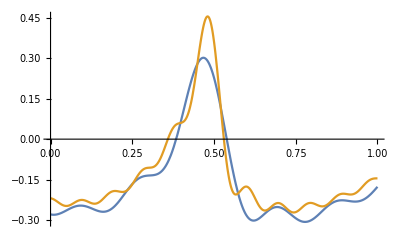

```mathematica
Plot[{%56,Sum[Term[i],{i,1,10}]//N//Simplify},{t,0,1}]
```

```mathematica
f[x_]=Tan[x]-1/x;
D[f[x],x]
```

1/x^2+Sec[x]^2

```mathematica
0.5-(-2.+tan[0.5])/(4.+tan'[0.5])//N
```

0.5-(1. (-2.+tan[0.5]))/(4.+tan'[0.5])

```mathematica
NestList[(#-f[#]/(D[f[x],x]/.x->#))&,0.1,4]
```

{0.1,0.198007,0.380696,0.65694,0.848918}

```mathematica
Clear[β]
```

```mathematica
For[i=1,i≤10,i++,β[i]=NestList[(#-f[#]/(D[f[x],x]/.x->#))&,1.0+(i-1)*π,4][[5]]]
```

```mathematica
?β
```

Global`β

β[1]=0.860334
 
β[2]=3.42562
 
β[3]=6.4373
 
β[4]=9.52933
 
β[5]=12.6453
 
β[6]=15.7713
 
β[7]=18.9024
 
β[8]=22.0365
 
β[9]=25.1724
 
β[10]=28.3096

```mathematica
10*π+1/(10*π)//N
```

31.4478

```mathematica
f[β[10]]
```

```mathematica
f[β[1]]
```

0.

```mathematica
Clear[A]
```

```mathematica
For[i=1,i≤10,i++,B[i]=A[i]/β[i]]
```

```mathematica
?A
```

Global`A

A[1][1]=1
 
A[1]=1.11913
 
A[2]=-0.151692
 
A[3]=0.0465941
 
A[4]=-0.0216682
 
A[5]=0.0123916
 
A[6]=-0.00799263
 
A[7]=0.00557415
 
A[8]=-0.00410589
 
A[9]=0.00314886
 
A[10]=-0.00249086

```mathematica
Sum[A[i]*Cos[β[i]*0.4],{i,1,10}]
```

0.998831

```mathematica
β1[n_]=(2n+1)/2*π
```

1/2 (1+2 n) π

```mathematica
B1[n_]=4/((2*n+1)*π)
```

4/((1+2 n) π)

```mathematica
Sum[B1[i]*Sin[β1[i]*0.5],{i,0,10}]//N
```

1.00182

```mathematica
Clear[A]
```

```mathematica
A[1][1]=1
```

1

```mathematica
A[1][1]
```

1

```mathematica
NIntegrate[Cos[β[1]x]^2,{x,0,1}]
```

0.787328